```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

```mathematica
StokesGraph[Q_,l_]:=
Module[{zeros,poles,z,x,y,i,zerosPlot,polesPlot,plotRange,stokes, antistokes},
zeros=NSolve[Q[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];
zerosPlot=ListPlot[Table[{Re[zeros⟦i⟧],Im[zeros⟦i⟧]},{i,1,Length[zeros]}],PlotStyle->Blue];

poles=NSolve[Q[z]^-1==0,z];
poles=Table[z/.poles⟦i⟧,{i,1,Length[poles]}];
polesPlot=ListPlot[Table[{Re[poles⟦i⟧],Im[poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red];

plotRange={{Min[Min[Re[zeros]],Min[Re[poles]]]-l,Max[Max[Re[zeros]],Max[Re[poles]]]+l},{Min[Min[Im[zeros]],Min[Im[poles]]]-l,Max[Max[Im[zeros]],Max[Im[poles]]]+l}};
stokes=StreamPlot[{Cos[-1/2 Arg[Q[x+ⅈ y]]],Sin[-1/2 Arg[Q[x+ⅈ y]]]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
antistokes=StreamPlot[{Cos[-(Arg[Q[x+ⅈ y]]+π)/2],Sin[-(Arg[Q[x+ⅈ y]]+π)/2]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧}];
{Show[stokes,zerosPlot,polesPlot,ImageSize->Large],Show[antistokes,zerosPlot,polesPlot,ImageSize->Large]}
];
```

1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))

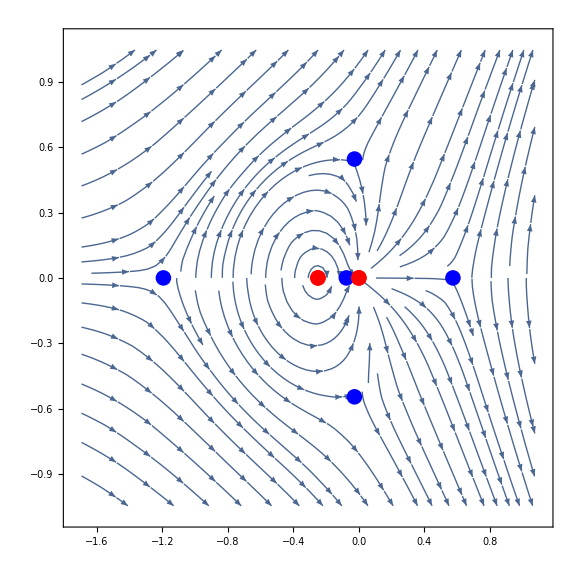
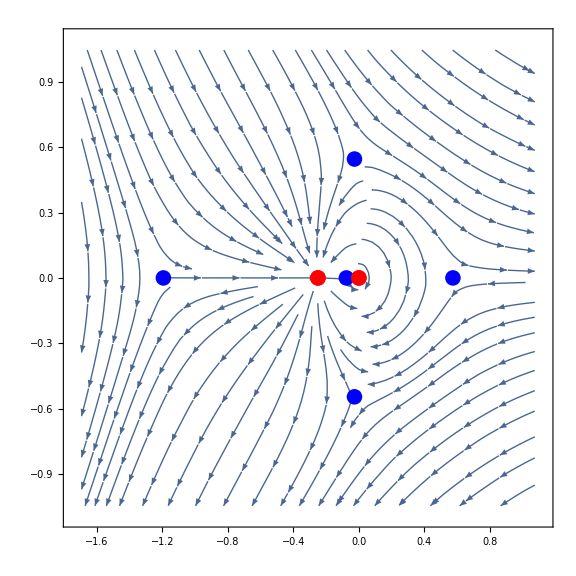

```mathematica
values={β->0.7,δ->0.5};
Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x][x]
StokesGraph[Function[z,%/.x->z/.values],0.5]//Quiet
Clear[values];
```

(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)

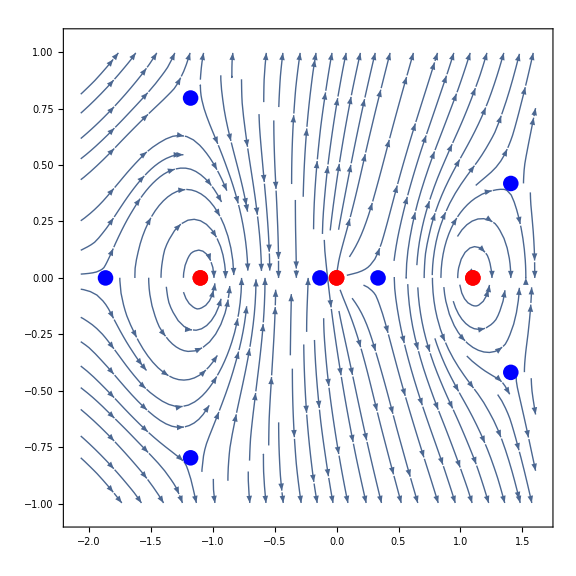
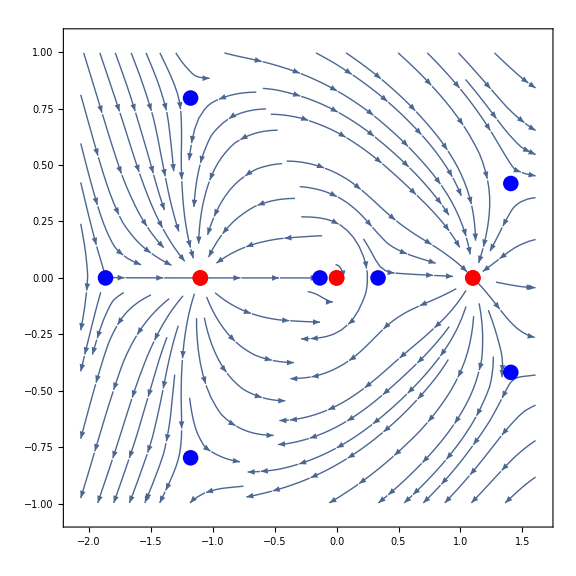

```mathematica
values={β->1.1,δ->1.1};
Q[-1/x(x^2+β^2)/(x^2-β^2),-(x+δ^2-β^2/x-(2β δ)/(x^2-β^2)),x][x]
StokesGraph[Function[z,%/.x->z/.values],0.2]//Quiet
Clear[values];
```

{-3.37718,-1.78165+0.637191 ⅈ,-1.78165-0.637191 ⅈ,0.432497,-0.242019}

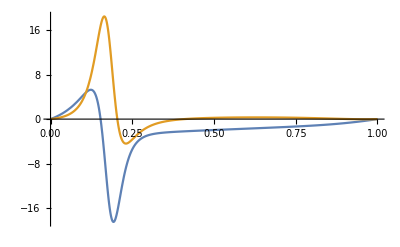

```mathematica
β=1;δ=1.5;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦4⟧;
b=zeros⟦3⟧;

Plot[{Re[potential[line[a,b][t]]],Im[potential[line[a,b][t]]]},{t,0,1},PlotRange->Full]

Clear[Amp,δ,β,a,b,c,d,e,ab,bc,cd,de,ac,ce,zeros,poles,potential];
```

{-2.16264,-0.574824+0.616715 ⅈ,-0.574824-0.616715 ⅈ,0.588607,-0.276316}

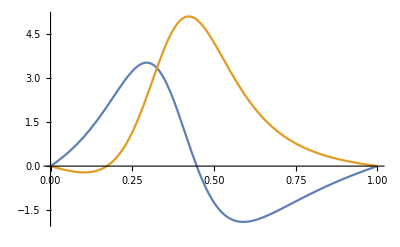

0.729742-2.00437 ⅈ

```mathematica
β=1;δ=1;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
c=zeros⟦1⟧;

Plot[{Re[potential[line[a,c][t]]],Im[potential[line[a,c][t]]]},{t,0,1},PlotRange->Full]
NIntegrate[-ⅈ (a-c)√(potential[s]/.s->line[a,c][t]),{t,0,1}]

Clear[Amp,δ,β,a,b,c,d,e,ab,bc,cd,de,ac,ce,zeros,poles,potential];
```

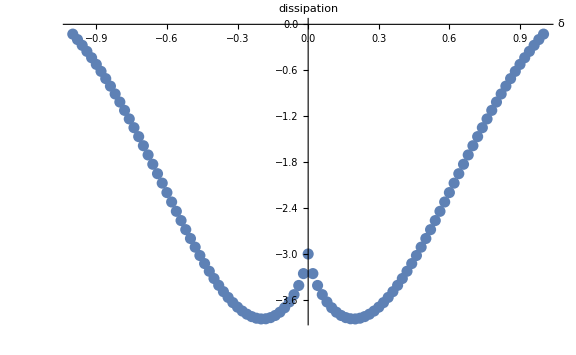

```mathematica
Dissipation={};
begining=-1;end=1;nstep=100;β=0;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=If[Length[zeros]>3,zeros⟦3⟧,zeros⟦1⟧];
(*b=-δ^2;*)
c=zeros⟦1⟧;

ac=If[a==c,0,NIntegrate[-ⅈ (a-c)√(potential[s]/.s->line[a,c][t]),{t,0,1}]];
(*bc=NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}];*)

R=ⅇ^(-2 (ac)) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->-ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->-ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,zeros,poles,potential];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Large]
```

{-4.04582,0.0229096+0.429944 ⅈ,0.0229096-0.429944 ⅈ}

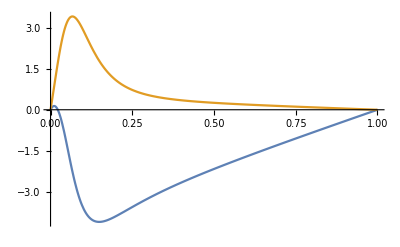

5.39848-1.39671 ⅈ

```mathematica
δ=2;
potential=Function[x,-3/(4 x^2)-x-δ^2];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦1⟧;

Plot[{Re[potential[line[a,b][t]]],Im[potential[line[a,b][t]]]},{t,0,1},PlotRange->Full]
NIntegrate[-ⅈ (a-b)√(potential[s]/.s->line[a,b][t]),{t,0,1}]

Clear[Amp,δ,β,a,b,c,d,e,ab,bc,cd,de,ac,ce,zeros,poles,potential];
```

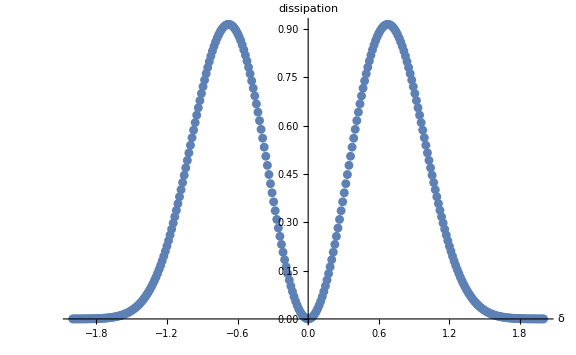

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;β=0;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

δ=0;
potential=Function[x,-3/(4 x^2)-x-δ^2];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦3⟧;
b=zeros⟦1⟧;

ab0=NIntegrate[-ⅈ (a-b)√(potential[s]/.s->line[a,b][t]),{t,0,1}];

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,-3/(4 x^2)-x-δ^2];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦3⟧;
b=zeros⟦1⟧;

ab=NIntegrate[-ⅈ (a-b)√(potential[s]/.s->line[a,b][t]),{t,0,1}];

R=ⅇ^(-2 ab) Subscript[s, 1]+Subscript[s, 2]/.{Subscript[s, 1]->2ⅈ ⅇ^(2ab0),Subscript[s, 2]->-ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,ab,ab0,potential,zeros];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]
```

{-1.35067,-0.614265+0.700222 ⅈ,-0.614265-0.700222 ⅈ,0.782674+0.422712 ⅈ,0.782674-0.422712 ⅈ,0.13692,-0.123069}

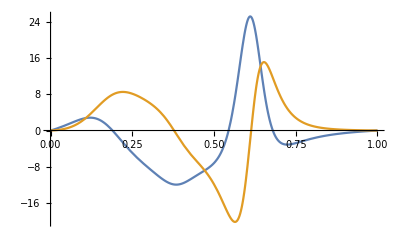

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.378891}. NIntegrate obtained 0.455628  - 3.24759\ ⅈ and 0.00317783 for the integral and error estimates.

0.455628-3.24759 ⅈ

```mathematica
δ=1;β=0.5;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦5⟧;
c=zeros⟦1⟧;

Plot[{Re[potential[line[a,c][t]]],Im[potential[line[a,c][t]]]},{t,0,1},PlotRange->Full]
NIntegrate[-ⅈ (a-c)√(potential[s]/.s->line[a,c][t]),{t,0,1}]

Clear[Amp,δ,β,a,b,c,d,e,ab,bc,cd,de,ac,ce,zeros,poles,potential];
```

{-1.35067,-0.614265+0.700222 ⅈ,-0.614265-0.700222 ⅈ,0.782674+0.422712 ⅈ,0.782674-0.422712 ⅈ,0.13692,-0.123069}

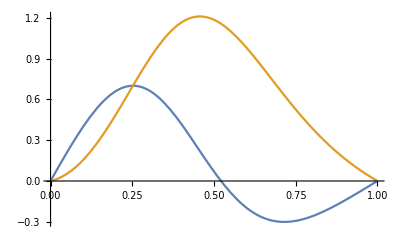

-0.0564011-0.779092 ⅈ

```mathematica
δ=1;β=0.5;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

b=zeros⟦3⟧;
c=zeros⟦1⟧;

Plot[{Re[potential[line[b,c][t]]],Im[potential[line[b,c][t]]]},{t,0,1},PlotRange->Full]
NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}]

Clear[Amp,δ,β,a,b,c,d,e,ab,bc,cd,de,ac,ce,zeros,poles,potential];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.357406}. NIntegrate obtained 0.208974  - 1.65148\ ⅈ and 0.000125813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.355453}. NIntegrate obtained 0.215363  - 1.64181\ ⅈ and 0.000158459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.349594}. NIntegrate obtained 0.227679  - 1.62389\ ⅈ and 0.000328247 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

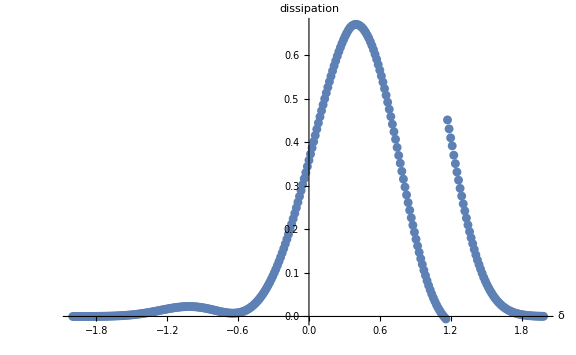

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
β=0.2;

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=zeros⟦5⟧;
b=zeros⟦3⟧;
c=zeros⟦1⟧;

ac=NIntegrate[-ⅈ (a-c)√(potential[s]/.s->line[a,c][t]),{t,0,1}];
bc=NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}];

R=ⅇ^(-2 ac) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->-ⅈ,Subscript[s, 2]->0.55,Subscript[s, 3]->-ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,potential,zeros];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]
```